```mathematica
sol3 = DSolve[{y'[x] + y[x]*Tan[x]== Sin[2x],y[0] == 2},y[x],x]
```

{{y[x]→-2 (-2 Cos[x]+Cos[x]^2)}}

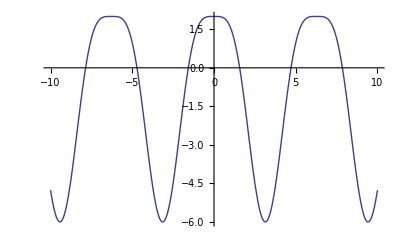

```mathematica
Plot[
Evaluate[
y[x] /. First[DSolve[{y'[x] + y[x]*Tan[x]== Sin[2x],y[0] == 2},y[x],x]]],{x,-10,10}]
```

```mathematica
sol1 = DSolve[{y''[x] + (b/1)y'[x] + (c/1)y[x] ==0,y[0] ==b,y'[0]==c},y[x],x]
```

{{y[x]→1/(2 √(b^2-4 c))(-b^2 ⅇ^(1/2 (-b-√(b^2-4 c)) x)+b √(b^2-4 c) ⅇ^(1/2 (-b-√(b^2-4 c)) x)-2 c ⅇ^(1/2 (-b-√(b^2-4 c)) x)+b^2 ⅇ^(1/2 (-b+√(b^2-4 c)) x)+b √(b^2-4 c) ⅇ^(1/2 (-b+√(b^2-4 c)) x)+2 c ⅇ^(1/2 (-b+√(b^2-4 c)) x))}}

```mathematica
y[x_,b_,c_] = y[x]/.sol1[[1]]
```

1/(2 √(b^2-4 c))(-b^2 ⅇ^(1/2 (-b-√(b^2-4 c)) x)+b √(b^2-4 c) ⅇ^(1/2 (-b-√(b^2-4 c)) x)-2 c ⅇ^(1/2 (-b-√(b^2-4 c)) x)+b^2 ⅇ^(1/2 (-b+√(b^2-4 c)) x)+b √(b^2-4 c) ⅇ^(1/2 (-b+√(b^2-4 c)) x)+2 c ⅇ^(1/2 (-b+√(b^2-4 c)) x))

```mathematica
Manipulate[Plot[Evaluate[y[x,b,c]],{x,-10,10}],{b,-10,10},{c,-10,10}]
```

```mathematica
sol4 = NDSolve[{x''[t] + a*x'[t]+(b^2 )*x[t]*(1-c*x[t]^2) == d*Cos[e*t],x[0]==x'[0]==0},{x,a,b,c,d,e},{t,-10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{b^2 x[t] (1-c x[t]^2)+a x'[t]+x''[t]==d Cos[f t],x[0]==x'[0]==0},{x},{t,-10}]